```mathematica
Needs["MSGCorep`"];
Needs["MagneticKP`"];
```

## Construct KP Model

```mathematica
showMLGCorep[{156,50},{1/3,1/3,0}]
```

MSG 156.50(P3m11'):  k-point name is K, for ,,HexaPrim
▶  k=(,,1/31/30) non-standard, k_BC=(,,-1/32/30)  [σ_v1]k_BC ⇔ k
Index |  |  | 1 | 2 | 3 | 4 | 5 | 6
Element |  |  | {E|000} | {C_3^+|000} | {C_3^-|000} | {σ_v1|000}' | {σ_v2|000}' | {σ_v3|000}'
Rotation
matrix |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | -1 | 0
1 | -1 | 0
0 | 0 | 1) | (-1 | 1 | 0
-1 | 0 | 0
0 | 0 | 1) | (-1 | 1 | 0
0 | 1 | 0
0 | 0 | 1) | (1 | 0 | 0
1 | -1 | 0
0 | 0 | 1) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | 1)
Spin(↓↑)
rotation
matrix |  |  | (1 | 0
0 | 1) | (1/2+(ⅈ √3)/2 | 0
0 | 1/2-(ⅈ √3)/2) | (1/2-(ⅈ √3)/2 | 0
0 | 1/2+(ⅈ √3)/2) | (0 | -1
1 | 0) | (0 | -1/2+(ⅈ √3)/2
1/2+(ⅈ √3)/2 | 0) | (0 | -1/2-(ⅈ √3)/2
1/2-(ⅈ √3)/2 | 0)
1 |  K_1  | a | 1 | 1 | 1 | 1 | 1 | 1
2 |  K_2  | a | 1 | ⅇ^(-(2 ⅈ π)/3) | ⅇ^((2 ⅈ π)/3) | 1 | ⅇ^((2 ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3)
3 |  K_3  | a | 1 | ⅇ^((2 ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3) | 1 | ⅇ^(-(2 ⅈ π)/3) | ⅇ^((2 ⅈ π)/3)
4 |  K_4  | a | 1 | ⅇ^(-(ⅈ π)/3) | ⅇ^((ⅈ π)/3) | 1 | ⅇ^((ⅈ π)/3) | ⅇ^(-(ⅈ π)/3)
5 |  K_5  | a | 1 | ⅇ^((ⅈ π)/3) | ⅇ^(-(ⅈ π)/3) | 1 | ⅇ^(-(ⅈ π)/3) | ⅇ^((ⅈ π)/3)
6 |  K_6  | a | 1 | -1 | -1 | 1 | -1 | -1

### We use Fraction Coordinates

```mathematica
input=interfaceRep[{156,50},"K",{2,3},"CartesianCoordinates"->False]
```

<|Unitary→<|{C_3^+|000}→{{{ⅇ^((2 ⅈ π)/3),0},{0,ⅇ^(-(2 ⅈ π)/3)}},{-kx-ky,kx,kz}}|>,Anitunitary→<|{σ_v1|000}'→{{{1,0},{0,1}},{kx,-kx-ky,-kz}}|>,lable→{K_2,K_3}|>

```mathematica
ham=kpHam[2,input]["ham"];MatrixForm[ham]
```

(C_(0,1)+C_(0,2)+(kx^2+kx ky+ky^2) C_(2,1)+(kx^2+kx ky+ky^2) C_(2,3)+kz^2 C_(2,5)+kz^2 C_(2,6) | (kx-(ⅈ kx)/(√3)-(2 ⅈ ky)/(√3)) C_(1,1)+(kx^2+ⅈ √3 kx^2-2 kx ky+2 ⅈ √3 kx ky-2 ky^2) C_(2,2)+(-ⅈ kx kz-(kx kz)/(√3)-(2 ky kz)/(√3)) C_(2,4)
(kx+(ⅈ kx)/(√3)+(2 ⅈ ky)/(√3)) C_(1,1)+(kx^2-ⅈ √3 kx^2-2 kx ky-2 ⅈ √3 kx ky-2 ky^2) C_(2,2)+(ⅈ kx kz-(kx kz)/(√3)-(2 ky kz)/(√3)) C_(2,4) | C_(0,1)-C_(0,2)+(kx^2+kx ky+ky^2) C_(2,1)+(-kx^2-kx ky-ky^2) C_(2,3)+kz^2 C_(2,5)-kz^2 C_(2,6))

## Read the vasp input file

### vaspEig[Full path of EIGENVAL file , Fermi energy, Spin, Start band , End band] For no SOC calculation Spin is always 1.

```mathematica
eigdata=vaspEig[NotebookDirectory[]<>"EIGENVAL",-0.0072,1,21,22];
```

## Initialization parameters

### hamshift is shift the Ham from {0,0,0} to K point

```mathematica
hamshift=ham/.{kx->kx-1/3,ky->ky-1/3};
bandManipulateWithVASP[hamshift,eigdata,"PlotRange"->{-2,3},"ManipulateRange"->{-4,5}]
```

Number of params:9

params:{C_(0,1),C_(0,2),C_(1,1),C_(2,1),C_(2,2),C_(2,3),C_(2,4),C_(2,5),C_(2,6)}

{C_(0,1)→0,C_(0,2)→0.19,C_(1,1)→4.33,C_(2,1)→4.33,C_(2,2)→0,C_(2,3)→0,C_(2,4)→0,C_(2,5)→0,C_(2,6)→0}

## Fitting the parameters

### fittingKP[Ham , eigdata, krange] eigdata is output of vaspEig krange is a list that Including the index of k-points you need to be fitted

```mathematica
fit=fittingKP[hamshift,eigdata,Range[50,70,5],{Subscript[C, 0,1]->0,Subscript[C, 0,2]->0.1900000000000004,Subscript[C, 1,1]->4.33,Subscript[C, 2,1]->4.33,Subscript[C, 2,2]->0,Subscript[C, 2,3]->0,Subscript[C, 2,4]->0,Subscript[C, 2,5]->0,Subscript[C, 2,6]->0}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

<|FittedParams→{C_(0,1)→0.000842276,C_(0,2)→-0.128035,C_(1,1)→4.79618,C_(2,1)→2.37998,C_(2,2)→1.24558,C_(2,3)→0.0212959,C_(2,4)→0.,C_(2,5)→0.,C_(2,6)→0.},LSQForInitParams→0.456114,LSQForFittedParams→0.0655846|>

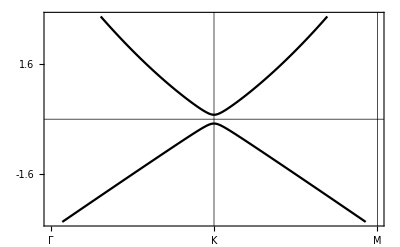

```mathematica
path={{{{0,0,0},{1/3,1/3,0}}/(2Pi),{"Γ","K"}},
{{{1/3,1/3,0},{0,0,0}}/(2Pi),{"K","M"}}};
bandplot[path,200,hamshift,fit["FittedParams"],"PlotRange"->{-3,3}]
```

```mathematica
SystemOpen[NotebookDirectory[]]
```